# Space Debris (Model H); color scheme : -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["Space-Debris-Model.nb",InsertResults->False];
myThickness=0.005;tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,.015}][##]&;
```

## global parameters

```mathematica
(***   b , sL , sR , betL , betR , tauL , tauR : benefit parameters                      ***)
(***   a , tauC , betC , sC                    : cost parameters                         ***)
(***   Ts                                      : s-time-scale parameter                  ***)
(***   rlim , λ , inov , α (efficiency)        : Ṡ parameters (λ is dummy)               ***)
eps=1.0*10^-15;
rLIM =0.155; iNOV=0.845; α = 1.75; tLIM=360;
nGRID=100;dGRID=0.01;intervalWIDTH=40;pGOAL=40;
```

## FIG-04

dedf4/color-grid-1-FSE-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt

10201

percentage of configs with 1     :     24.39

percentage of configs with 2     :     28.47

percentage of configs with 3     :     38.43

percentage of configs with 4     :     8.71

percentage of configs with s = 0 :     52.86

percentage of configs with s = 1 :     47.14

dedf4/color-grid-2-FSE-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt

10201

percentage of configs with 1     :     25.97

percentage of configs with 2     :     0.98

percentage of configs with 3     :     0.01

percentage of configs with 4     :     73.04

percentage of configs with s = 0 :     26.95

percentage of configs with s = 1 :     73.05

dedf4/color-grid-3-FSE-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt

10201

percentage of configs with 1     :     31.61

percentage of configs with 2     :     34.49

percentage of configs with 3     :     32.57

percentage of configs with 4     :     1.33

percentage of configs with s = 0 :     66.10

percentage of configs with s = 1 :     33.90

dedf4/color-grid-4-FSE-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt

10201

percentage of configs with 1     :     49.59

percentage of configs with 2     :     6.71

percentage of configs with 3     :     0.01

percentage of configs with 4     :     43.69

percentage of configs with s = 0 :     56.30

percentage of configs with s = 1 :     43.70

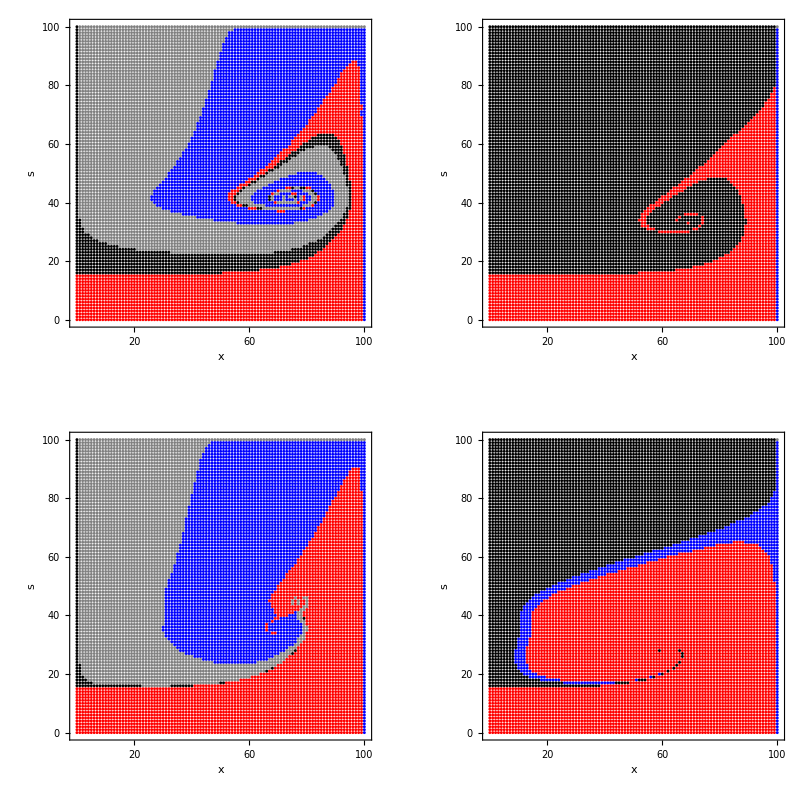

```mathematica
filname="dedf4/color-grid-1-FSE-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt";pl11=PlotGRID[nGRID,filname];
filname="dedf4/color-grid-2-FSE-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt";pl12=PlotGRID[nGRID,filname];
filname="dedf4/color-grid-3-FSE-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt";pl21=PlotGRID[nGRID,filname];
filname="dedf4/color-grid-4-FSE-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.txt";pl22=PlotGRID[nGRID,filname];
GraphicsGrid[{{pl11, pl12}, {pl21,pl22}},ImageSize->800]
```